```mathematica
Quit
```

XY 平面的 参数方程

```mathematica
{x0[X_,Y_],y0[X_,Y_],z0[X_,Y_]}={1/2 Cos[2 π X] (2+Cos[2 π Y]),1/2 (2+Cos[2 π Y]) Sin[2 π X],1/2 Sin[2 π Y]}
```

{1/2 Cos[2 π X] (2+Cos[2 π Y]),1/2 (2+Cos[2 π Y]) Sin[2 π X],1/2 Sin[2 π Y]}

```mathematica
ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0,1},{Y,0,1},PlotRange->All]
```

-Graphics3D-

参考曲面

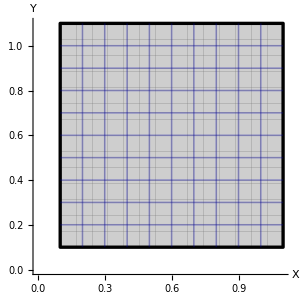

```mathematica
Ref1=ParametricPlot[{X,Y},{X,0.1,1.1},{Y,0.1,1.1},Mesh->9,PlotStyle->Directive[RGBColor[0.618,0.618,0.618],Specularity[White,50],Opacity[0.5]],MeshStyle->Directive[Thickness[.004],Darker[Blue]],BoundaryStyle->Directive[Thickness[.008],Black],PerformanceGoal->"Quality",ImageSize->300,AxesLabel->{"X","Y"},LabelStyle->{FontSize->20,FontFamily->"Times",Black},Frame->False]
```

目标曲面

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0.1,1.1},{Y,0.1,1.1},Mesh->None,PlotStyle->Directive[RGBColor[0.618,0.618,1],Specularity[White,50],Opacity[0.5]],BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Table[{θ1,C1,0},{C1,2/10,10/10,1/10}];
Curve1=ParametricPlot3D[{%},{θ1,1/10,11/10},PlotStyle->Directive[Thickness[.005],Red]]
```

-Graphics3D-

```mathematica
Table[{C2,θ2,0},{C2,2/10,10/10,1/10}];
Curve2=ParametricPlot3D[{%},{θ2,1/10,11/10},PlotStyle->Directive[Thickness[.005],Blue]]
```

-Graphics3D-

```mathematica
Ref1=ParametricPlot3D[{X,Y,0},{X,0.1,1.1},{Y,0.1,1.1},PlotStyle->Directive[RGBColor[0.618,0.618,0.618],Specularity[White,50],Opacity[0.4]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality"];
```

```mathematica
Show[Curve1,Curve2,Ref1,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Curve1=ParametricPlot3D[Table[{x0[X,Y0],y0[X,Y0],z0[X,Y0]},{Y0,2/10,10/10,1/10}],{X,0.1,1.1},PlotStyle->Directive[Thickness[.005],Red],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Curve2=ParametricPlot3D[Table[{x0[X0,Y],y0[X0,Y],z0[X0,Y]},{X0,2/10,10/10,1/10}],{Y,0.1,1.1},PlotStyle->Directive[Thickness[.005],Blue],PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0.1,1.1},{Y,0.1,1.1},PlotStyle->Directive[RGBColor[0.618,0.618,1],Specularity[White,80],Opacity[0.8],Glow[RGBColor[0.618,0.618,1]]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality"];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

-Graphics3D-

去掉反光

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0.1,1.1},{Y,0.1,1.1},PlotStyle->Directive[RGBColor[0.618,0.618,1],Opacity[0.8]],Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality",ViewProjection->"Orthographic",(*ColorFunction->White,*)Lighting->{{"Point",White,{0,0,1}},{"Directional",RGBColor[1,1,1],{1,1,1}},{"Directional",RGBColor[1,1,1],{5,-6,1}}}];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->600,PerformanceGoal->"Quality",MaxRecursion-> 10]
```

-Graphics3D-

```mathematica
Cur1=ParametricPlot3D[{x0[X,Y],y0[X,Y],z0[X,Y]},{X,0.1,1.1},{Y,0.1,1.1},(*PlotStyle->Directive[RGBColor[0.618,0.618,1],Specularity[White,80],Opacity[0.4]],*)Mesh->None,BoundaryStyle->Directive[Thickness[.008],Black],Boxed->False,Axes->False,PerformanceGoal->"Quality"];
Show[Cur1,Curve1,Curve2,Boxed->False,Axes->False,ImageSize->500,PerformanceGoal->"Quality",MaxRecursion-> 10,ViewProjection->"Orthographic"]
```

-Graphics3D-